```mathematica
EdgeList[WheelGraph[6]]
```

{1<->2,1<->3,1<->4,1<->5,1<->6,2<->3,2<->6,3<->4,4<->5,5<->6}

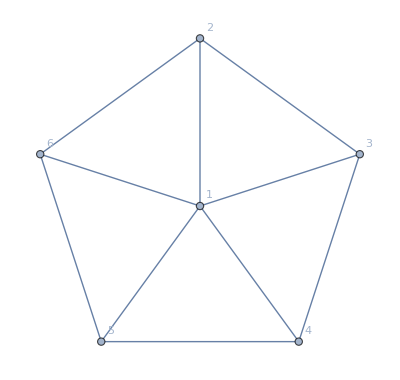

```mathematica
Graph[WheelGraph[6],GraphLayout->"TutteEmbedding", VertexLabels->"Name"]
```

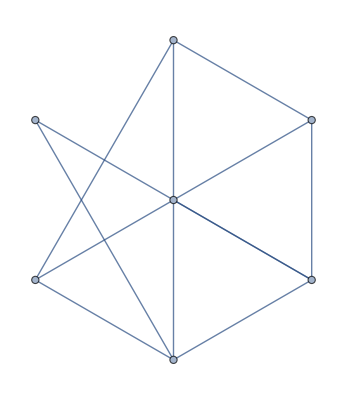

```mathematica
EdgeAdd[WheelGraph[6],{3<->7,4<->7}]
```

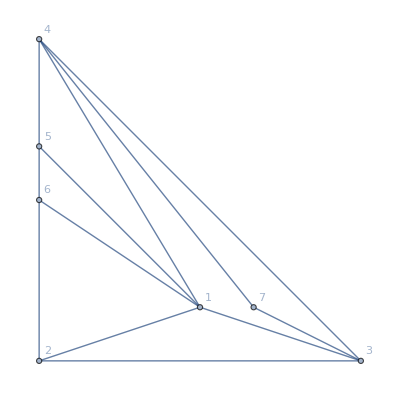
-Graphics-
{2,3,4,5,6}→(-30+8 I2-2 I24+2 I24x3-I24x35+I24x35x6-I24x36+I24x36x5-I24x3x5+I24x3x5x6-I24x3x6+I24x5-I24x5x6+I24x6-2 I25+I25x3-I25x36+I25x36x4-I25x3x4+I25x3x46+I25x3x4x6-I25x3x6+I25x4-I25x46-I25x4x6+2 I25x6-4 I2x3+I2x35-I2x35x4+I2x35x46+I2x35x4x6-I2x35x6+2 I2x36-I2x36x4+I2x36x4x5-I2x36x5+2 I2x3x4-I2x3x46+I2x3x46x5-I2x3x4x5+I2x3x4x5x6-I2x3x4x6+I2x3x5-I2x3x5x6+2 I2x3x6-2 I2x4+I2x46-I2x46x5+I2x4x5-I2x4x5x6+I2x4x6-2 I2x5+2 I2x5x6-4 I2x6+8 I3-2 I35+2 I35x4-I35x46-I35x4x6+I35x6-2 I36+I36x4-I36x4x5+I36x5-4 I3x4+I3x46-I3x46x5+2 I3x4x5-I3x4x5x6+I3x4x6-2 I3x5+I3x5x6-2 I3x6+8 I4-2 I46+2 I46x5-4 I4x5+2 I4x5x6-2 I4x6+8 I5-4 I5x6+8 I6) O17+(-90+24 I2-4 I24+2 I24x3-I24x35+I24x35x6-I24x36+I24x36x5-I24x3x5+I24x3x5x6-I24x3x6+2 I24x5-2 I24x5x6+2 I24x6-6 I25+2 I25x3-2 I25x36+I25x36x4-I25x3x4+I25x3x46+I25x3x4x6-2 I25x3x6+2 I25x4-2 I25x46-2 I25x4x6+6 I25x6-8 I2x3+2 I2x35-I2x35x4+I2x35x46+I2x35x4x6-2 I2x35x6+4 I2x36-I2x36x4+I2x36x4x5-2 I2x36x5+2 I2x3x4-I2x3x46+I2x3x46x5-I2x3x4x5+I2x3x4x5x6-I2x3x4x6+2 I2x3x5-2 I2x3x5x6+4 I2x3x6-4 I2x4+2 I2x46-2 I2x46x5+2 I2x4x5-2 I2x4x5x6+2 I2x4x6-6 I2x5+6 I2x5x6-12 I2x6+16 I3-4 I35+2 I35x4-I35x46-I35x4x6+2 I35x6-4 I36+I36x4-I36x4x5+2 I36x5-4 I3x4+I3x46-I3x46x5+2 I3x4x5-I3x4x5x6+I3x4x6-4 I3x5+2 I3x5x6-4 I3x6+16 I4-4 I46+4 I46x5-8 I4x5+4 I4x5x6-4 I4x6+24 I5-12 I5x6+24 I6) O1x7

```mathematica
With[{g=EdgeAdd[WheelGraph[6],{3<->7,4<->7}],s={2,3,4,5,6}},
Column[{Graph[g,GraphLayout->"PlanarEmbedding", VertexLabels->"Name"],
Framed[s->With[{form=CalculateInOutFormulaFull[g,s]},MyRewrite5[form]]
]
}
]
]
```

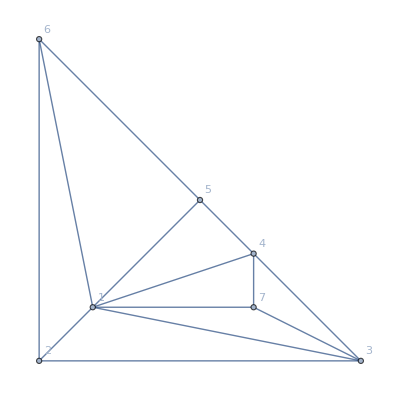
-Graphics-
{2,3,4,5,6}→(-90+24 I2-4 I24+2 I24x3-I24x35+I24x35x6-I24x36+I24x36x5-I24x3x5+I24x3x5x6-I24x3x6+2 I24x5-2 I24x5x6+2 I24x6-6 I25+2 I25x3-2 I25x36+I25x36x4-I25x3x4+I25x3x46+I25x3x4x6-2 I25x3x6+2 I25x4-2 I25x46-2 I25x4x6+6 I25x6-8 I2x3+2 I2x35-I2x35x4+I2x35x46+I2x35x4x6-2 I2x35x6+4 I2x36-I2x36x4+I2x36x4x5-2 I2x36x5+2 I2x3x4-I2x3x46+I2x3x46x5-I2x3x4x5+I2x3x4x5x6-I2x3x4x6+2 I2x3x5-2 I2x3x5x6+4 I2x3x6-4 I2x4+2 I2x46-2 I2x46x5+2 I2x4x5-2 I2x4x5x6+2 I2x4x6-6 I2x5+6 I2x5x6-12 I2x6+16 I3-4 I35+2 I35x4-I35x46-I35x4x6+2 I35x6-4 I36+I36x4-I36x4x5+2 I36x5-4 I3x4+I3x46-I3x46x5+2 I3x4x5-I3x4x5x6+I3x4x6-4 I3x5+2 I3x5x6-4 I3x6+16 I4-4 I46+4 I46x5-8 I4x5+4 I4x5x6-4 I4x6+24 I5-12 I5x6+24 I6) O1x7

```mathematica
With[{g=EdgeAdd[WheelGraph[6],{3<->7,4<->7,1<->7}],s={2,3,4,5,6}},
Column[{Graph[g,GraphLayout->"PlanarEmbedding", VertexLabels->"Name"],
Framed[s->With[{form=CalculateInOutFormulaFull[g,s]},MyRewrite5[form]]
]
}
]
]
```

```mathematica
(-90+24 I2-4 I24+2 I24x3-I24x35+I24x35x6-I24x36+I24x36x5-I24x3x5+I24x3x5x6-I24x3x6+2 I24x5-2 I24x5x6+2 I24x6-6 I25+2 I25x3-2 I25x36+I25x36x4-I25x3x4+I25x3x46+I25x3x4x6-2 I25x3x6+2 I25x4-2 I25x46-2 I25x4x6+6 I25x6-8 I2x3+2 I2x35-I2x35x4+I2x35x46+I2x35x4x6-2 I2x35x6+4 I2x36-I2x36x4+I2x36x4x5-2 I2x36x5+2 I2x3x4-I2x3x46+I2x3x46x5-I2x3x4x5+I2x3x4x5x6-I2x3x4x6+2 I2x3x5-2 I2x3x5x6+4 I2x3x6-4 I2x4+2 I2x46-2 I2x46x5+2 I2x4x5-2 I2x4x5x6+2 I2x4x6-6 I2x5+6 I2x5x6-12 I2x6+16 I3-4 I35+2 I35x4-I35x46-I35x4x6+2 I35x6-4 I36+I36x4-I36x4x5+2 I36x5-4 I3x4+I3x46-I3x46x5+2 I3x4x5-I3x4x5x6+I3x4x6-4 I3x5+2 I3x5x6-4 I3x6+16 I4-4 I46+4 I46x5-8 I4x5+4 I4x5x6-4 I4x6+24 I5-12 I5x6+24 I6)-(-90+24 I2-4 I24+2 I24x3-I24x35+I24x35x6-I24x36+I24x36x5-I24x3x5+I24x3x5x6-I24x3x6+2 I24x5-2 I24x5x6+2 I24x6-6 I25+2 I25x3-2 I25x36+I25x36x4-I25x3x4+I25x3x46+I25x3x4x6-2 I25x3x6+2 I25x4-2 I25x46-2 I25x4x6+6 I25x6-8 I2x3+2 I2x35-I2x35x4+I2x35x46+I2x35x4x6-2 I2x35x6+4 I2x36-I2x36x4+I2x36x4x5-2 I2x36x5+2 I2x3x4-I2x3x46+I2x3x46x5-I2x3x4x5+I2x3x4x5x6-I2x3x4x6+2 I2x3x5-2 I2x3x5x6+4 I2x3x6-4 I2x4+2 I2x46-2 I2x46x5+2 I2x4x5-2 I2x4x5x6+2 I2x4x6-6 I2x5+6 I2x5x6-12 I2x6+16 I3-4 I35+2 I35x4-I35x46-I35x4x6+2 I35x6-4 I36+I36x4-I36x4x5+2 I36x5-4 I3x4+I3x46-I3x46x5+2 I3x4x5-I3x4x5x6+I3x4x6-4 I3x5+2 I3x5x6-4 I3x6+16 I4-4 I46+4 I46x5-8 I4x5+4 I4x5x6-4 I4x6+24 I5-12 I5x6+24 I6)
```

0

```mathematica
With[{g=WheelGraph[6],s={2,3,4,5,6}},
Column[{Graph[g,GraphLayout->"TutteEmbedding", VertexLabels->"Name"],
Framed[s->With[{form=CalculateInOutFormulaFull[g,s]},MyRewrite5[form]]
]
}
]
]
```

-Graphics-
{2,3,4,5,6}→(-30+8 I2-2 I24+2 I24x3-I24x35+I24x35x6-I24x36+I24x36x5-I24x3x5+I24x3x5x6-I24x3x6+I24x5-I24x5x6+I24x6-2 I25+I25x3-I25x36+I25x36x4-I25x3x4+I25x3x46+I25x3x4x6-I25x3x6+I25x4-I25x46-I25x4x6+2 I25x6-4 I2x3+I2x35-I2x35x4+I2x35x46+I2x35x4x6-I2x35x6+2 I2x36-I2x36x4+I2x36x4x5-I2x36x5+2 I2x3x4-I2x3x46+I2x3x46x5-I2x3x4x5+I2x3x4x5x6-I2x3x4x6+I2x3x5-I2x3x5x6+2 I2x3x6-2 I2x4+I2x46-I2x46x5+I2x4x5-I2x4x5x6+I2x4x6-2 I2x5+2 I2x5x6-4 I2x6+8 I3-2 I35+2 I35x4-I35x46-I35x4x6+I35x6-2 I36+I36x4-I36x4x5+I36x5-4 I3x4+I3x46-I3x46x5+2 I3x4x5-I3x4x5x6+I3x4x6-2 I3x5+I3x5x6-2 I3x6+8 I4-2 I46+2 I46x5-4 I4x5+2 I4x5x6-2 I4x6+8 I5-4 I5x6+8 I6) O1

```mathematica
((-30+8 I2-2 I24+2 I24x3-I24x35+I24x35x6-I24x36+I24x36x5-I24x3x5+I24x3x5x6-I24x3x6+I24x5-I24x5x6+I24x6-2 I25+I25x3-I25x36+I25x36x4-I25x3x4+I25x3x46+I25x3x4x6-I25x3x6+I25x4-I25x46-I25x4x6+2 I25x6-4 I2x3+I2x35-I2x35x4+I2x35x46+I2x35x4x6-I2x35x6+2 I2x36-I2x36x4+I2x36x4x5-I2x36x5+2 I2x3x4-I2x3x46+I2x3x46x5-I2x3x4x5+I2x3x4x5x6-I2x3x4x6+I2x3x5-I2x3x5x6+2 I2x3x6-2 I2x4+I2x46-I2x46x5+I2x4x5-I2x4x5x6+I2x4x6-2 I2x5+2 I2x5x6-4 I2x6+8 I3-2 I35+2 I35x4-I35x46-I35x4x6+I35x6-2 I36+I36x4-I36x4x5+I36x5-4 I3x4+I3x46-I3x46x5+2 I3x4x5-I3x4x5x6+I3x4x6-2 I3x5+I3x5x6-2 I3x6+8 I4-2 I46+2 I46x5-4 I4x5+2 I4x5x6-2 I4x6+8 I5-4 I5x6+8 I6))-(-30+8 I2-2 I24+2 I24x3-I24x35+I24x35x6-I24x36+I24x36x5-I24x3x5+I24x3x5x6-I24x3x6+I24x5-I24x5x6+I24x6-2 I25+I25x3-I25x36+I25x36x4-I25x3x4+I25x3x46+I25x3x4x6-I25x3x6+I25x4-I25x46-I25x4x6+2 I25x6-4 I2x3+I2x35-I2x35x4+I2x35x46+I2x35x4x6-I2x35x6+2 I2x36-I2x36x4+I2x36x4x5-I2x36x5+2 I2x3x4-I2x3x46+I2x3x46x5-I2x3x4x5+I2x3x4x5x6-I2x3x4x6+I2x3x5-I2x3x5x6+2 I2x3x6-2 I2x4+I2x46-I2x46x5+I2x4x5-I2x4x5x6+I2x4x6-2 I2x5+2 I2x5x6-4 I2x6+8 I3-2 I35+2 I35x4-I35x46-I35x4x6+I35x6-2 I36+I36x4-I36x4x5+I36x5-4 I3x4+I3x46-I3x46x5+2 I3x4x5-I3x4x5x6+I3x4x6-2 I3x5+I3x5x6-2 I3x6+8 I4-2 I46+2 I46x5-4 I4x5+2 I4x5x6-2 I4x6+8 I5-4 I5x6+8 I6)
```

0

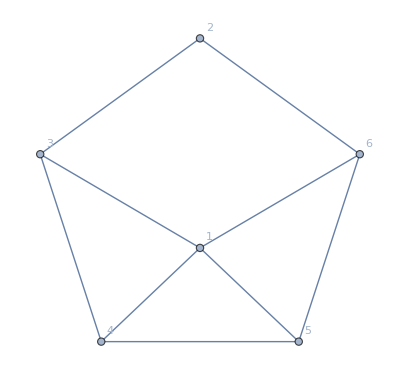
-Graphics-
{2,3,4,5,6}→(-22+8 I2-2 I24+2 I24x3-I24x35+I24x35x6-I24x36+I24x36x5-I24x3x5+I24x3x5x6-I24x3x6+I24x5-I24x5x6+I24x6-2 I25+I25x3-I25x36+I25x36x4-I25x3x4+I25x3x46+I25x3x4x6-I25x3x6+I25x4-I25x46-I25x4x6+2 I25x6-4 I2x3+I2x35-I2x35x4+I2x35x46+I2x35x4x6-I2x35x6+2 I2x36-I2x36x4+I2x36x4x5-I2x36x5+2 I2x3x4-I2x3x46+I2x3x46x5-I2x3x4x5+I2x3x4x5x6-I2x3x4x6+I2x3x5-I2x3x5x6+2 I2x3x6-2 I2x4+I2x46-I2x46x5+I2x4x5-I2x4x5x6+I2x4x6-2 I2x5+2 I2x5x6-4 I2x6+4 I3-I35+I35x4-2 I3x4+I3x4x5-I3x5+6 I4-I46+I46x5-3 I4x5+I4x5x6-I4x6+6 I5-2 I5x6+4 I6) O1

```mathematica
With[{g=EdgeDelete[WheelGraph[6],{1<->2}],s={2,3,4,5,6}},
Column[{Graph[g,GraphLayout->"TutteEmbedding", VertexLabels->"Name"],
Framed[s->With[{form=CalculateInOutFormulaFull[g,s]},MyRewrite5[form]]
]
}
]
]
```

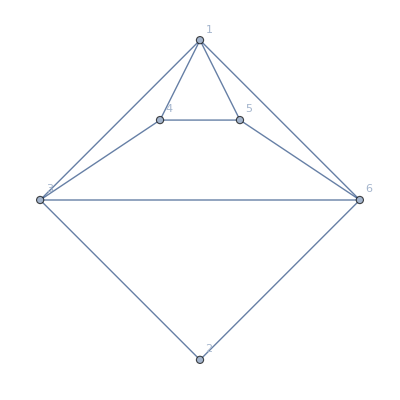
-Graphics-
{2,3,4,5,6}→(-28+14 I2-4 I24+2 I24x3-I24x35+I24x35x6-I24x3x5+I24x3x5x6-I24x3x6+2 I24x5-I24x5x6+I24x6-4 I25+I25x3-I25x3x4+I25x3x46+I25x3x4x6-I25x3x6+2 I25x4-I25x46-I25x4x6+2 I25x6-4 I2x3+I2x35-I2x35x4+I2x35x46+I2x35x4x6-I2x35x6+2 I2x3x4-I2x3x46+I2x3x46x5-I2x3x4x5+I2x3x4x5x6-I2x3x4x6+I2x3x5-I2x3x5x6+2 I2x3x6-4 I2x4+I2x46-I2x46x5+2 I2x4x5-I2x4x5x6+I2x4x6-4 I2x5+2 I2x5x6-4 I2x6+4 I3-I35+I35x4-2 I3x4+I3x4x5-I3x5+8 I4-I46+I46x5-4 I4x5+I4x5x6-I4x6+8 I5-2 I5x6+4 I6) O1

```mathematica
With[{g=EdgeAdd[EdgeDelete[WheelGraph[6],{1<->2}],{3<->6}],s={2,3,4,5,6}},
Column[{Graph[g,GraphLayout->"TutteEmbedding", VertexLabels->"Name"],
Framed[s->With[{form=CalculateInOutFormulaFull[g,s]},MyRewrite5[form]]
]
}
]
]
```

```mathematica
Simplify[(-30+8 I2-2 I24+2 I24x3-I24x35+I24x35x6-I24x36+I24x36x5-I24x3x5+I24x3x5x6-I24x3x6+I24x5-I24x5x6+I24x6-2 I25+I25x3-I25x36+I25x36x4-I25x3x4+I25x3x46+I25x3x4x6-I25x3x6+I25x4-I25x46-I25x4x6+2 I25x6-4 I2x3+I2x35-I2x35x4+I2x35x46+I2x35x4x6-I2x35x6+2 I2x36-I2x36x4+I2x36x4x5-I2x36x5+2 I2x3x4-I2x3x46+I2x3x46x5-I2x3x4x5+I2x3x4x5x6-I2x3x4x6+I2x3x5-I2x3x5x6+2 I2x3x6-2 I2x4+I2x46-I2x46x5+I2x4x5-I2x4x5x6+I2x4x6-2 I2x5+2 I2x5x6-4 I2x6+8 I3-2 I35+2 I35x4-I35x46-I35x4x6+I35x6-2 I36+I36x4-I36x4x5+I36x5-4 I3x4+I3x46-I3x46x5+2 I3x4x5-I3x4x5x6+I3x4x6-2 I3x5+I3x5x6-2 I3x6+8 I4-2 I46+2 I46x5-4 I4x5+2 I4x5x6-2 I4x6+8 I5-4 I5x6+8 I6)-(-28+14 I2-4 I24+2 I24x3-I24x35+I24x35x6-I24x3x5+I24x3x5x6-I24x3x6+2 I24x5-I24x5x6+I24x6-4 I25+I25x3-I25x3x4+I25x3x46+I25x3x4x6-I25x3x6+2 I25x4-I25x46-I25x4x6+2 I25x6-4 I2x3+I2x35-I2x35x4+I2x35x46+I2x35x4x6-I2x35x6+2 I2x3x4-I2x3x46+I2x3x46x5-I2x3x4x5+I2x3x4x5x6-I2x3x4x6+I2x3x5-I2x3x5x6+2 I2x3x6-4 I2x4+I2x46-I2x46x5+2 I2x4x5-I2x4x5x6+I2x4x6-4 I2x5+2 I2x5x6-4 I2x6+4 I3-I35+I35x4-2 I3x4+I3x4x5-I3x5+8 I4-I46+I46x5-4 I4x5+I4x5x6-I4x6+8 I5-2 I5x6+4 I6)]
```

-2-6 I2+2 I24-I24x36+I24x36x5-I24x5+2 I25-I25x36+I25x36x4-I25x4+2 I2x36-I2x36x4+I2x36x4x5-I2x36x5+2 I2x4-I2x4x5+2 I2x5+4 I3-I35+I35x4-I35x46-I35x4x6+I35x6-2 I36+I36x4-I36x4x5+I36x5-2 I3x4+I3x46-I3x46x5+I3x4x5-I3x4x5x6+I3x4x6-I3x5+I3x5x6-2 I3x6-I46+I46x5+I4x5x6-I4x6-2 I5x6+4 I6

```mathematica
Sort[ListofVars[(-30+8 I2-2 I24+2 I24x3-I24x35+I24x35x6-I24x36+I24x36x5-I24x3x5+I24x3x5x6-I24x3x6+I24x5-I24x5x6+I24x6-2 I25+I25x3-I25x36+I25x36x4-I25x3x4+I25x3x46+I25x3x4x6-I25x3x6+I25x4-I25x46-I25x4x6+2 I25x6-4 I2x3+I2x35-I2x35x4+I2x35x46+I2x35x4x6-I2x35x6+2 I2x36-I2x36x4+I2x36x4x5-I2x36x5+2 I2x3x4-I2x3x46+I2x3x46x5-I2x3x4x5+I2x3x4x5x6-I2x3x4x6+I2x3x5-I2x3x5x6+2 I2x3x6-2 I2x4+I2x46-I2x46x5+I2x4x5-I2x4x5x6+I2x4x6-2 I2x5+2 I2x5x6-4 I2x6+8 I3-2 I35+2 I35x4-I35x46-I35x4x6+I35x6-2 I36+I36x4-I36x4x5+I36x5-4 I3x4+I3x46-I3x46x5+2 I3x4x5-I3x4x5x6+I3x4x6-2 I3x5+I3x5x6-2 I3x6+8 I4-2 I46+2 I46x5-4 I4x5+2 I4x5x6-2 I4x6+8 I5-4 I5x6+8 I6)],SymbolComp]
```

{I2,I3,I4,I5,I6,I24,I25,I35,I36,I46,I2x3,I2x4,I2x5,I2x6,I3x4,I2x3x4,I25x3x4,I3x5,I24x3x5,I2x3x5,I3x6,I2x3x6,I25x3x6,I24x3x6,I24x3,I4x5,I3x4x5,I36x4x5,I2x3x4x5,I2x4x5,I2x36x4x5,I24x5,I4x6,I35x4x6,I2x3x4x6,I25x4x6,I3x4x6,I2x4x6,I2x35x4x6,I25x3x4x6,I24x6,I25x3,I35x4,I2x35x4,I25x4,I5x6,I4x5x6,I3x4x5x6,I2x5x6,I2x4x5x6,I2x3x5x6,I2x35x6,I25x6,I24x5x6,I3x5x6,I35x6,I2x3x4x5x6,I24x3x5x6,I24x35x6,I2x36x4,I36x4,I25x36x4,I46x5,I3x46x5,I2x46x5,I2x36x5,I36x5,I2x3x46x5,I24x36x5,I24x35,I2x35,I2x36,I25x36,I24x36,I35x46,I2x3x46,I25x46,I3x46,I2x46,I2x35x46,I25x3x46}

```mathematica
Sort[ListofVars[-2-6 I2+2 I24-I24x36+I24x36x5-I24x5+2 I25-I25x36+I25x36x4-I25x4+2 I2x36-I2x36x4+I2x36x4x5-I2x36x5+2 I2x4-I2x4x5+2 I2x5+4 I3-I35+I35x4-I35x46-I35x4x6+I35x6-2 I36+I36x4-I36x4x5+I36x5-2 I3x4+I3x46-I3x46x5+I3x4x5-I3x4x5x6+I3x4x6-I3x5+I3x5x6-2 I3x6-I46+I46x5+I4x5x6-I4x6-2 I5x6+4 I6],SymbolComp]
```

{I2,I3,I6,I24,I25,I35,I36,I46,I2x4,I2x5,I3x4,I3x5,I3x6,I36x4x5,I2x4x5,I24x5,I3x4x5,I2x36x4x5,I4x6,I35x4x6,I3x4x6,I25x4,I35x4,I5x6,I3x4x5x6,I4x5x6,I3x5x6,I35x6,I2x36x4,I36x4,I25x36x4,I3x46x5,I2x36x5,I46x5,I36x5,I24x36x5,I2x36,I25x36,I24x36,I35x46,I3x46}